Початково-крайова задача екології
метод скінченних елементів ( 17.12.12)

Жуки:
1. неправильний обрахунок базисних функцій (19.12.12)
2. неоптимальний обрахунок базисних функцій

Що покращити:
	1.  врахувати при обчисленні локальних матриць симетричність білінійних форм
	2.  реалізацію алгоритму перевірки приналежності точки трикутнику ::: isPointIntriangle, наявна isPointInTriangleArea -затратніша
	              // http://math.stackexchange.com/questions/51326/determining-if-an-arbitrary-point-lies-inside-a-triangle-defined-by-three-points
	3.

## 1. Постановка задачі

Задача Діріхле для еліптичного рівняння на двовимірній області 

	L[u] = -μΔu + β∇u +σu = f		Ω=[0,1]x[0,1]			(1)
				u|_Γ = 0						(2)
				
Ми розглядаємо задачу зі сталими коефіцієнтами, тому 

	u=(x,y),	f=f(x,y),	μ=const,   β=const,   σ=const.		(3)

```mathematica
(* Блок ініціалізації вхідних параметрів *)
μ=Function[{x,y},100];
β=Function[{x,y},1];
σ=Function[{x,y},1];
f=Function[{x,y},100000];
```

## 2. Триангуляція

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Generation of node file

.node files

First line: 		<# of vertices> <dimension (must be 2)> <# of attributes> <# of boundary markers (0 or 1)>
Remaining lines: 	<vertex #> <x> <y> [attributes] [boundary marker]

Blank lines and comments prefixed by `#’ may be placed anywhere. Vertices must be numbered consecutively, starting from one or zero.

The attributes, which are typically floating-point values of physical quantities (such as mass or conductivity) associated with the nodes of a finite element mesh, are copied unchanged to the output mesh. If -q, -a, -u, or -s is selected, each new Steiner point added to the mesh will have quantities assigned to it by linear interpolation.

If the fourth entry of the first line is `1’, the last column of the remainder of the file is assumed to contain boundary markers. Boundary markers are used to identify boundary vertices and vertices resting on PSLG segments. The .node files produced by Triangle contain boundary markers in the last column unless they are suppressed by the -B switch.

```mathematica
$pathToFile="square.node"
stmp = OpenWrite[$pathToFile];

(* <# of vertices> <dimension (must be 2)> <# of attributes> <# of boundary markers (0 or 1)> *)
WriteString[stmp,"4 2 0 0 \n"];

(* == <vertex #> <x> <y> [attributes] [boundary marker] *)
WriteString[stmp, "1 0.0 0.0 \n"];
WriteString[stmp, "2 1.0 0.0 \n"];
WriteString[stmp, "3 1.0 1.0 \n"];
WriteString[stmp, "4 0.0 1.0 \n"];
Close[stmp];
```

square.node

### Execution of triangulation program

```mathematica
$triangleCmd= "triangle ";
commandToRun =$triangleCmd<>" square.node";
Run[commandToRun];
```

### Data input

```mathematica
triangles=Import["square.1.ele","Table"];
(*Results in list of vetrices forming triangles*)
triangles=Delete[triangles,-1];
triangles=Delete[triangles,1];
For[i=1,i<=Length[triangles],i++,
triangles[[i]]=Delete[triangles[[i]],1]
];
triangles;

nodes=Import["square.1.node","Table"];
(*Results in list of vetrices*)
nodes=Delete[nodes,-1];
nodes=Delete[nodes,1];
For[i=1,i<=Length[nodes],i++,
nodes[[i]]=Delete[nodes[[i]],1];
];
nodes;
```

### Visualization

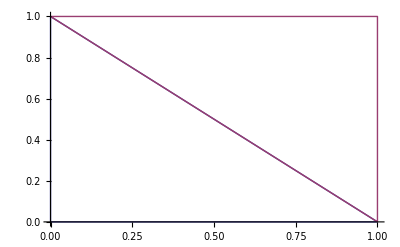

```mathematica
(*starightforward nonoptimized method*)
(*make list of edges grouped by triangles [[tris]] 
and ListLinePlot[{tris[[1]],..,tris[[n]]] them.*)

getVertexXY:=Function[{triangleNumber,vertexNumber},
Delete[nodes[[triangles[[triangleNumber,vertexNumber]]]],-1]
];
(*list of triangle vertecies for complete triangle drawing*)
toFormTriangle={1,2,3,1};

(* array of triangles *)
tris={{}};
For[i=1,i<=Length[triangles],i++,
self={{}};
For[j=1,j<=Length[toFormTriangle],j++,
self=Append[self,getVertexXY[i,toFormTriangle[[j]]]];
];
self=Delete[self,1];
tris=Append[tris,self];
]
tris=Delete[tris,1];

ListLinePlot[tris]
```

```mathematica
Length[tris]
```

2

## 3. Використання скінченноелеметного підходу

Застосувавши до (1) метод віртуальних функцій та використавши формулу інтегрування частинами, отримуємо:

				(-μΔu + β∇u +σu -f, v) = -(μ∇u, v)|_Γ+(∇μ∇u + β∇u +σu -f, v),		(4)

де перший доданок справа рівний нулю в силу (2). Введемо ж білінійну форму та лінійний функціонал

				A(u,v) = (∇μ∇u + β∇u +σu , v),	< l, v > = < f, v >,			(5)

та отримаємо в результаті:

							A(u,v) = < f, v >.					(6)

З огляду на білінійну форму та умову (2), мусимо константувати, що функція v з (6) 
мусить належати хоча б простору V=H_0^1(Ω).

Конкретизуємо простір V. Виберемо щільний підпростір V_h  такий, що
							
							dim  V_h  = N < + ∞.					(7)

Виберемо в ньому базис - систему лінійнонезалежних функцій {φ_j}_(j=1)^N. Виразимо через цей базис
розв’язок - функцію u:

						u(x)=∑_(j=0)^N c_j φ_j,
						
де ∀с_j∈ ℝ - невідомі коефіцієнти, які слід знайти. Застосувавши метод Гальоркіна, перепишимо рівняння (6)
у вигляді (8)

						∑_(j=0)^N c_j A(φ_j,φ_i)=(f,φ_i)		i=0,..,N.		(8)

### Вибір базових функцій

Нехай трикутник К утворено вершинами  A_i(x_i, y_i), i=1,2,3,   які занумеровано в порядку їхнього обходу проти годинникової стрілки. Сторону трикутника, яка лежить навпроти вершини A_i, будемо позначати S_i. Введемо до розгляду на цьому трикутнику набір сталих

					a_i:=x_j y_m-x_m y_j,
b_i:=y_j-y_m,
c_i:=-(x_j-x_m),     i,j,m=1,2,3,    i→j→m→i			(9)

та лінійних функцій

					L_i(x,y):=(a_i+b_i x+c_i y)/(2|K|)           ∀(x,y)∈K,     i=1,2,3.		(10)

Систему функцій (10) будемо називати барицентричними координатами на трикутнику K.

```mathematica
(* дві функції, остання з яких повертає відповідь на питання:
		Точка належить трикутнику чи ні ? *)
pointSign=Function[{a,b,c},
q=(a[[1]]-c[[1]])*(b[[2]]-c[[2]]);
w=(b[[1]]-c[[1]])*(a[[2]]-c[[2]]);
q-w
];

isPointInTriangle=Function[{triangleNumber,x,y},
v1=getVertexXY[triangleNumber,1];
v2=getVertexXY[triangleNumber,2];
v3=getVertexXY[triangleNumber,3];

b1 =pointSign[{x,y},v1,v2]<0;
b2 =pointSign[{x,y},v2,v3]<0;
b3 =pointSign[{x,y},v3,v1]<0;

Print[ToString[v1]<>" "<>ToString[v2]<>" "<>ToString[v3]];

(b1==b2 &&b2==b3)
];

isPointInTriangleArea=Function[{triangleNumber,x,y},
{xa,ya}={x,y};
{xb,yb}=getVertexXY[triangleNumber,2];
{xc,yc}=getVertexXY[triangleNumber,3];
areaA=1/2*Abs[xa*yc-xa*yb+xb*ya-xb*yc+xc*yb-xc*ya];
{xa,ya}=getVertexXY[triangleNumber,1];
{xb,yb}={x,y};
areaB=1/2*Abs[xa*yc-xa*yb+xb*ya-xb*yc+xc*yb-xc*ya];
{xb,yb}=getVertexXY[triangleNumber,2];
{xc,yc}={x,y};

areaC=1/2*Abs[xa*yc-xa*yb+xb*ya-xb*yc+xc*yb-xc*ya];
(areaA+areaB+areaC)==triangleArea[triangleNumber]
];

(* функція, яка повертає площу вказаного трикутника *)
triangleArea:=Function[{triangleNumber},
{xa,ya}=getVertexXY[triangleNumber,1];
{xb,yb}=getVertexXY[triangleNumber,2];
{xc,yc}=getVertexXY[triangleNumber,3];

1/2*Abs[xa*yc-xa*yb+xb*ya-xb*yc+xc*yb-xc*ya]
];

(* функція, еквівалентна до (10), приймає номер трикутника, індекс фукнції L та (x,y) *)
getBaricentric=Function[{triangleNumber,index,x,y,derivative},

(* присвоєння відповідних значень змінним, згідно з (9) *)

Switch[index,
1,
{xj,yj}=getVertexXY[triangleNumber,2];
{xm,ym}=getVertexXY[triangleNumber,3];
Break,
2,
{xj,yj}=getVertexXY[triangleNumber,3];
{xm,ym}=getVertexXY[triangleNumber,1];
Break,
3,
{xj,yj}=getVertexXY[triangleNumber,1];
{xm,ym}=getVertexXY[triangleNumber,2];
Break
];

a=xj*ym-xm*yj;
b=yj-ym;
c=-(xj-xm);

result=0;
If[isPointInTriangleArea[triangleNumber,x,y],
Switch[derivative,
0, result=a+b*x+c*y,
1, result=b,
2, result=c],
0
]
result/(2*triangleArea[triangleNumber])
];
```

```mathematica
Plot3D[getBaricentric[1,1,x,y,0]+getBaricentric[1,2,x,y,0]+getBaricentric[1,3,x,y,0],{x,0,1},{y,0,1-x}]
```

-Graphics3D-

```mathematica
Length[triangles]
```

2

```mathematica
777
triangles[[73]]
```

777

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

{{4,1,2},{2,3,4}}⟦73⟧

```mathematica
{408,409,410}
asd={nodes[[29,1;;2]],nodes[[4,1;;2]],nodes[[46,1;;2]],nodes[[29,1;;2]]}
ListLinePlot[asd]
```

{408,409,410}

Part::partw: Part 29 of {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} does not exist.

Part::partw: Part 46 of {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} does not exist.

Part::partw: Part 29 of {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{{0,0,1},{1,0,1},{1,1,1},{0,1,1}}⟦29,1;;2⟧,{0,1},{{0,0,1},{1,0,1},{1,1,1},{0,1,1}}⟦46,1;;2⟧,{{0,0,1},{1,0,1},{1,1,1},{0,1,1}}⟦29,1;;2⟧}

Part::partw: Part 29 of {{0., 0., 1.}, {1., 0., 1.}, {1., 1., 1.}, {0., 1., 1.}} does not exist.

Part::partw: Part 46 of {{0., 0., 1.}, {1., 0., 1.}, {1., 1., 1.}, {0., 1., 1.}} does not exist.

Part::partw: Part 29 of {{0., 0., 1.}, {1., 0., 1.}, {1., 1., 1.}, {0., 1., 1.}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
getBaricentric[73,1,0.20,0.08,0]
```

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 2 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xj, yj} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 3 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xm, ym} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 2 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::shape: Lists {xb, yb} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
NIntegrate[getBaricentric[73,1,x,y,0],{x,0,1},{y,0,1},Method->"MonteCarlo"]
```

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 2 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xj, yj} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 3 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xm, ym} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 2 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::shape: Lists {xb, yb} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

NIntegrate[getBaricentric[73,1,x,y,0],{x,0,1},{y,0,1},Method→MonteCarlo]

```mathematica
Plot3D[getBaricentric[73,1,x,y,0],{x,0,1},{y,0,1}]
```

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 2 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xj, yj} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 3 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xm, ym} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 73 of {{4, 1, 2}, {2, 3, 4}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 73, 2 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::shape: Lists {xb, yb} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics3D-

## 4. Реалізація МСЕлементів

### Чисельне інтегрування на трикутниках

[1] Appropriate Gaussian quadrature formulae for triangles \\ F.Hussain, M.S. Karim, R. Ahamad - available here

```mathematica
GGauss2={0.5283121635*10^-1,0.1971687836,0.5283121635*10^-1,0.1971687836};
uGauss2={0.1666666667,0.6220084679,0.4465819874*10^-1,0.1666666667};
vGauss2={0.7886751346,0.2113248654,0.7886751346,0.2113248654};

GGauss3={0.9876542474*10^-1,0.1391378575*10^-1,0.1095430035,0.6172839460*10^-1,0.8696116674*10^-2,0.6846438175*10^-1,0.6172839460*10^-1,0.8696116674*10^-2,0.6846438175*10^-1};
uGauss3={0.2500000000,0.5635083269*10^-1,0.4436491673,0.4436491673,0.1000000000,0.7872983346,0.5635083269*10^-1,0.1270166538*10^-1,0.1000000000};
vGauss3={0.5000000000,0.8872983346,0.1127016654,0.5000000000,0.8872983346,0.1127016654,0.5000000000,0.8872983346,0.1127016654};

convertX=Function[{triangleNumber,ξ,η},
x1=getVertexXY[triangleNumber,1][[1]];
x2=getVertexXY[triangleNumber,2][[1]];
x3=getVertexXY[triangleNumber,3][[1]];

x1+1/2(x2-x1)(1+ξ)+1/4(x3-x1)(1-ξ)(1+η)
];
convertY=Function[{triangleNumber,ξ,η},
y1=getVertexXY[triangleNumber,1][[2]];
y2=getVertexXY[triangleNumber,2][[2]];
y3=getVertexXY[triangleNumber,3][[2]];

y1+1/2(y2-y1)(1+ξ)+1/4(y3-y1)(1-ξ)(1+η)
];

calculateLocalTriagleIntegralA=Function[{triangleNumber,index1,index2,func},
result=0;
For[i=1,i≤9,i++,
xLoc=uGauss3[[i]];
yLoc=vGauss3[[i]];

adder=GGauss3[[i]]*func[triangleNumber,index1,convertX[triangleNumber,xLoc,yLoc],convertY[triangleNumber,xLoc,yLoc],0];
Print[adder];
result+= adder;
]
result*triangleArea[triangleNumber]
];
```

```mathematica
Timing[NIntegrate[subIntegralFunctionA[1,1,1,x,y],{x,0,1},{y,0,1}]]
```

{0.021169,12.5208}

```mathematica
Timing[NIntegrate[subIntegralFunctionA[1,1,2,x,y],{x,0,1},{y,0,1},Method->"LocalAdaptive"]]
```

{0.016638,0.}

```mathematica
Plot3D[subIntegralFunctionA[1,1,3,x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Timing[NIntegrate[subIntegralFunctionA[1,1,3,x,y],{x,0,1},{y,0,1},MaxRecursion->3]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.032988,0.}

```mathematica
calculateLocalTriagleIntegralA[1,1,1,getBaricentric]
```

0.000868055

9.83574×10^-6

0.0016684

0.00029854

5.59179×10^-6

0.000152414

0.000858867

6.72919×10^-6

0.00272878

0.101185 Null

```mathematica
NIntegrate[getBaricentric[8,1,x,y,0],{x,0,1},{y,0,1},MaxRecursion->6]//Timing
```

Part::partw: Part 8 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 8, 2 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xj, yj} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 8 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 8, 3 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xm, ym} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 8 of {{4, 1, 2}, {2, 3, 4}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 8, 2 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::shape: Lists {xb, yb} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

{0.011603,NIntegrate[getBaricentric[8,1,x,y,0],{x,0,1},{y,0,1},MaxRecursion→6]}

```mathematica
k=1;index1=2;index2=2;
Timing[NIntegrate[μ[x,y]*gradientBasicFunctions[k,index1,x,y]*gradientBasicFunctions[k,index2,x,y]+β[x,y]*gradientBasicFunctions[k,index1,x,y]*getBaricentric[k,index2,x,y,0]+σ[x,y]*getBaricentric[k,index1,x,y,0]*getBaricentric[k,index2,x,y,0],{x,0,1},{y,0,1}]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.015719,0.}

```mathematica
calculateLocalTriagleIntegralA[1,1,1,subIntegralFunctionA]
```

0.0987654 (0.410645+50 Switch[0.28125,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.0139138 (0.473766+50 Switch[0.445237,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.109543 (0.384203+50 Switch[0.154763,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.0617284 (0.432874+50 Switch[0.208632,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.00869612 (0.474964+50 Switch[0.424642,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.0684644 (0.453931+50 Switch[0.0591684,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.0617284 (0.389001+50 Switch[0.353868,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.00869612 (0.472569+50 Switch[0.465832,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

0.0684644 (0.320286+50 Switch[0.250358,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};])

1/2 Null (0.800358+0.0684644 (0.320286+50 Switch[0.250358,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};]))

### Формування СЛАР

Формування СЛАР типу (8) можливе двома шляхами: з фіксованими трикутниками та з фіксованими комірками СЛАР. Використовуючи перший підхід, ми по черзі обходимо всі трикутники і додаємо у комірки, номери яких відповідають номерам вершин, що входять у трикутник, обраховані скалярні добутки відповідних функцій L_i. У другому випадку ми фіксуємо комірку і відповідну їй пару  вершин та обчислюємо для трикутників, які містять це ребро, відповідні скалярні добутки. Перший метод є ефективніший, коли йдеться про обчислення коефіцієнтів матриці: доступ до кожного трикутника відбувається тільки раз, та не потрібно створювати складні структури для зберігання кожного трикутника та прилеглих до нього.

```mathematica
(* ініціалізація глобальної СЛАР *)

n= Length[nodes];
globalA = Table[0,{i,1,n},{j,1,n}];
globalB = Table[0,{i,1,n}] ;

(* формування локальної СЛАР *)

gradientBasicFunctions=Function[{k,index,x,y},
getBaricentric1[k,index,x,y,1]+getBaricentric1[k,index,x,y,2]
];

subIntegralFunctionA=Function[{k,index1,index2,x,y},μ[x,y]*gradientBasicFunctions[k,index1,x,y]*gradientBasicFunctions[k,index2,x,y]+β[x,y]*gradientBasicFunctions[k,index1,x,y]*getBaricentric[k,index2,x,y,0]+σ[x,y]*getBaricentric1[k,index1,x,y,0]*getBaricentric1[k,index2,x,y,0]
];

subIntegralFunctionB=Function[{k,index1,index2,x,y},
f[x,y]*getBaricentric1[k,index2,x,y,0]
];

localToGlobalA=Function[{local,nodeList},
For[i=1,i<=Length[local],i++,
For[j=1,j<=Length[local],j++,
n1=nodeList[[i]];
n2=nodeList[[j]];
globalA[[n1,n2]]=local[[i,j]];
]
]
];

localToGlobalB=Function[{local,nodeList},
For[i=1,i<=Length[local],i++,
n1=nodeList[[i]];
globalB[[n1]]=local[[i]];
]
];

Print["Mark 1"];
For[k=1,k<=Length[triangles],k++,
localA=Table[0,{ia,1,3},{ja,1,3}];
localB=Table[0,{ia,1,3}];
globalNodes=triangles[[k]];
Print["Mark 2"];
localA//MatrixForm;
(* заповнення локальної матриці *)
For[iLoc=1,iLoc<=Length[localA],iLoc++,
For[jLoc=1,jLoc<=Length[localA],jLoc++,
Print["Mark "<>ToString[iLoc*10+jLoc]<>" "<>ToString[ΔNIntegrateA[k,iLoc,jLoc,subIntegralFunctionA]]];
self=ΔNIntegrateA[k,iLoc,jLoc,subIntegralFunctionA];
localA[[iLoc,jLoc]]=self;
];
self=ΔNIntegrateA[k,iLoc,jLoc,subIntegralFunctionB];
localB[[iLoc]]=self;
]
localToGlobalA[localA,globalNodes];
localToGlobalB[localB,globalNodes];
]

For[i=1,i<=Length[nodes],i++,
If[nodes[[i,3]]≠0,
self=10^20;
globalA[[i,i]]=self;
];
];

globalA // MatrixForm
globalB//MatrixForm

(* виведення локальної матрички *)
(* розподілення елементів локальної СЛАР по глобальній *)
```

Mark 1

Mark 2

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, μ[x, y]\ gradientBasicFunctions[k, index1, x, y]\ gradientBasicFunctions[k, index2, x, y] + β[x, y]\ « 1 »\ getBaricentric[k, « 3 », 0] + σ[x, y]\ getBaricentric1[k, index1, x, y, 0]\ getBaricentric1[k, index2, x, y, 0]][« 1 »].

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, μ[x, y]\ gradientBasicFunctions[k, index1, x, y]\ gradientBasicFunctions[k, index2, x, y] + β[x, y]\ « 1 »\ getBaricentric[k, « 3 », 0] + σ[x, y]\ getBaricentric1[k, index1, x, y, 0]\ getBaricentric1[k, index2, x, y, 0]][« 1 »].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 11      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 12      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 13      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 21      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 22      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 23      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 31      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 32      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 33      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0., 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                          3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                               3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

Mark 2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 11      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 12      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 13      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 21      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 22      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 23      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 31      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 32      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Mark 33      Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 0.5]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][0.5, 1.]   Function[{k, index1, index2, x, y}, μ[x, y] gradientBasicFunctions[k, index1, x, y] gradientBasicFunctions[k, index2, x, y] + β[x, y] gradientBasicFunctions[k, index1, x, y] getBaricentric[k, index2, x, y, 0] + σ[x, y] getBaricentric1[k, index1, x, y, 0] getBaricentric1[k, index2, x, y, 0]][1., 0.5]
0. + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------ + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                           3                                                                                                                                                                                                                                                                                                              3                                                                                                                                                                                                                                                                                                              3
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,1.]

Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][1.,0.5]

result

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, μ[x, y]\ gradientBasicFunctions[k, index1, x, y]\ gradientBasicFunctions[k, index2, x, y] + β[x, y]\ « 1 »\ getBaricentric[k, « 3 », 0] + σ[x, y]\ getBaricentric1[k, index1, x, y, 0]\ getBaricentric1[k, index2, x, y, 0]][« 1 »].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

(100000000000000000000 | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]) | 0 | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5])
1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]) | 100000000000000000000 | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]) | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5])
0 | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]) | 100000000000000000000 | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5])
1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]) | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]) | 1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][1.,0.5]) | 100000000000000000000)

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0]][0., 0.5].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0]][0.5, 0.].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0]][0.5, 0.5].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

(1/2 (0.+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.,0.5]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5])
1/2 (0.+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][1.,0.5])
1/2 (0.+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][1.,0.5])
1/2 (0.+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,0.5]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][0.5,1.]+1/3 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0]][1.,0.5]))

```mathematica
subIntegralFunctionA[5,3,1,0.5,0.5]
```

Part::partw: Part 5 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 5, 2 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xb, yb} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 5 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 5, 3 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xc, yc} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 5 of {{4, 1, 2}, {2, 3, 4}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 5, 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::shape: Lists {xa, ya} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate

```mathematica
globalA[[1,1]]=NIntegrate[subIntegralFunctionA[1,2,3,x,y],{x,0,1},{y,0,1},Method->"LocalAdaptive"]
```

0.

```mathematica
Timing[NIntegrate[getBaricentric[5,3,x,y,1]*getBaricentric[5,3,x,y,0],{x,0,1},{y,0,1}]]
```

Part::partw: Part 5 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 5, 1 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xj, yj} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 5 of {{4, 1, 2}, {2, 3, 4}} does not exist.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 5, 2 ⟧ is neither an integer nor a list of integers.

Set::shape: Lists {xm, ym} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

Part::partw: Part 5 of {{4, 1, 2}, {2, 3, 4}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{4, 1, 2}, {2, 3, 4}} ⟦ 5, 2 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::shape: Lists {xb, yb} and {{0, 0, 1}, {1, 0, 1}, {1, 1, 1}, {0, 1, 1}} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

{0.011685,NIntegrate[getBaricentric[5,3,x,y,1] getBaricentric[5,3,x,y,0],{x,0,1},{y,0,1}]}

### Розв’язування СЛАР

```mathematica
u =LinearSolve[globalA,globalB]
```

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, μ[x, y]\ gradientBasicFunctions[k, index1, x, y]\ gradientBasicFunctions[k, index2, x, y] + β[x, y]\ « 1 »\ getBaricentric[k, « 3 », 0] + σ[x, y]\ getBaricentric1[k, index1, x, y, 0]\ getBaricentric1[k, index2, x, y, 0]][« 1 »].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

{«1»}

```mathematica
solution=Function[{x,y},
For[k=1,k<=Length[triangles],k++,
If[isPointInTriangle[k,x,y],
self=0;
For[i=1,i≤3,i++,
verticeNumber=triangles[[k,i]];
self+=getBaricentric[k,i,x,y,0]*u[[verticeNumber]];
]
,0]
]];
```

### Візуалізація розв’язку

```mathematica
Plot3D[solution[x,y],{x,0,1},{y,0,1}]
```

{0, 1} {0, 0} {1, 0}

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0., 0.5].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0.5, 0.].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0.5, 0.5].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

{0, 1} {0, 0} {1, 0}

{1, 0} {1, 1} {0, 1}

-Graphics3D-

```mathematica
xyz={{}};
For[i=1,i<=Length[nodes],i++,
self=nodes[[i]];
alf={self[[1]],self[[2]],u[[i]]};
xyz=Append[xyz,alf];
]
xyz=Delete[xyz,1]
```

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0., 0.5].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0.5, 0.].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0.5, 0.5].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

{{0,0,-1. ((2.×10^20 (0.+0.333333 Function[{k,index1,index2,x,y},f[x,y] «1»][0.,0.5]+«19» «1»[«1»]+0.333333 Function[{k,index1,index2,x,y},f[x,y] getBaricentric1[k,index2,x,y,0.]][0.5,0.5]))/(0.+0.333333 «1»+«1»+0.333333 Function[{k,index1,index2,x,y},«1»][0.5,0.5])^2-(1. (0.+«2»+«1»))/(0.+«1»+«1»+«19» «1»)+(«1»)/(«1»)+(1. («1») («1»))/((0.+«19» «1»[0.,«4»]+«1»+0.333333 «1») «1»))},«3»}

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0., 0.5].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0.5, 0.].

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, f[x, y]\ getBaricentric1[k, index2, x, y, 0.]][0.5, 0.5].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

```mathematica
{{0,0,-5.350760456668127},{1,0,3.8100757144758237},{1,1,-2.8424645841087215},{0,1,0.011116969836101233},{0.5,0.5,3.9602969393482654},{0,0.5,0.9862234801756943},{0.5,0,-0.9000922674015751},{1,0.5,0.2302609468800111},{0.5,1,-1.056548632562763}}
```

{{0,0,-5.35076},{1,0,3.81008},{1,1,-2.84246},{0,1,0.011117},{0.5,0.5,3.9603},{0,0.5,0.986223},{0.5,0,-0.900092},{1,0.5,0.230261},{0.5,1,-1.05655}}

```mathematica
Get["DiscreteMath`ComputationalGeometry`"]
TriangularSurfacePlot[xyz,ViewPoint->{2,5,2}]
```

General::newpkg: "DiscreteMath`ComputationalGeometry`" is now available as the "Computational Geometry Package". See the Compatibility Guide for updating information.

Compile::moptx: Method option "Optimization" in CompilationOptions is not one of {"ExpressionOptimization", "InlineCompiledFunctions", "InlineExternalDefinitions"}.

TriangularSurfacePlot[{«1»},ViewPoint→{2,5,2}]

### Інший спосіб визначення лінійного барицентричного базису на трикутнику

```mathematica
(* функція, яка повертає площу трикутника *)
triangleAreaPoint:=Function[{triangleNumber,index,x,y,derivative},
{xa,ya}=getVertexXY[triangleNumber,1];
{xb,yb}=getVertexXY[triangleNumber,2];
{xc,yc}=getVertexXY[triangleNumber,3];

Switch[index,
1,1/2,
2,{xb,yb}={xc,yc};{xc,yc}={xa,ya};,
3,{xc,yc}={xb,yb};{xb,yb}={xa,ya};
]

Switch[derivative,
0,1/2*Abs[x*yc-x*yb+xb*y-xb*yc+xc*yb-xc*y],
1,1/2*Abs[yc-yb],
2,1/2*Abs[xb-xc]
]

];

getBaricentric1=Function[{triangleNumber,index,x,y,derivative},
If[isPointInTriangleArea[triangleNumber,x,y],
triangleAreaPoint[triangleNumber,index,x,y,derivative]/triangleArea[triangleNumber],
0
]
];

Timing[Plot3D[getBaricentric1[1,1,x,y,0]/triangleArea[1],{x,0,1},{y,0,1}]]
Timing[Plot3D[getBaricentric1[1,1,x,y,0],{x,0,1},{y,0,1}]]
```

{0.213629,-Graphics3D-}

{0.175051,-Graphics3D-}

### Tries on integration techniques

http://anhngq.wordpress.com/2010/02/19/numerical-quadrature-over-triangles/

```mathematica
---------------------------- GOOD -------------
```

```mathematica
ΔNIntegrateA=Function[{triangleNumber,index1,index2,func},
b1={0.5,0.0,0.5};
b2={0.0,0.5,0.5};
b3={0.5,0.5,0.0};
wi={1/3,1/3,1/3};
result=0.0;
fun[x1_,y1_]:=func[triangleNumber,index1,index2,x1,y1];

For[nti=1,nti≤Length[wi],nti++,
xloc=b1[[nti]]*getVertexXY[triangleNumber,1][[1]]+b2[[nti]]*getVertexXY[triangleNumber,2][[1]]+b3[[nti]]*getVertexXY[triangleNumber,3][[1]];
yloc=b1[[nti]]*getVertexXY[triangleNumber,1][[2]]+b2[[nti]]*getVertexXY[triangleNumber,2][[2]]+b3[[nti]]*getVertexXY[triangleNumber,3][[2]];
result+=wi[[nti]]*func[xloc,yloc];
Print[func[xloc,yloc]];
];
Print["result"];

triangleArea[triangleNumber]*result
];
ΔNIntegrateA[1,1,2,subIntegralFunctionA]
```

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, μ[x, y]\ gradientBasicFunctions[k, index1, x, y]\ gradientBasicFunctions[k, index2, x, y] + β[x, y]\ « 1 »\ getBaricentric[k, « 3 », 0] + σ[x, y]\ getBaricentric1[k, index1, x, y, 0]\ getBaricentric1[k, index2, x, y, 0]][« 1 »].

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5]

Function::fpct: Too many parameters in {k, index1, index2, x, y} to be filled from Function[{k, index1, index2, x, y}, μ[x, y]\ gradientBasicFunctions[k, index1, x, y]\ gradientBasicFunctions[k, index2, x, y] + β[x, y]\ « 1 »\ getBaricentric[k, « 3 », 0] + σ[x, y]\ getBaricentric1[k, index1, x, y, 0]\ getBaricentric1[k, index2, x, y, 0]][« 1 »].

General::stop: Further output of Function :: fpct will be suppressed during this calculation.

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]

Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]

result

1/2 (0.+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.,0.5]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.]+1/3 Function[{k,index1,index2,x,y},μ[x,y] gradientBasicFunctions[k,index1,x,y] gradientBasicFunctions[k,index2,x,y]+β[x,y] gradientBasicFunctions[k,index1,x,y] getBaricentric[k,index2,x,y,0]+σ[x,y] getBaricentric1[k,index1,x,y,0] getBaricentric1[k,index2,x,y,0]][0.5,0.5])

```mathematica
-------------------------------------------------
```

```mathematica
ΔNIntegrate=Function[{triangleNumber,index1,index2,der1,der2},
b1={0.5,0.0,0.5};
b2={0.0,0.5,0.5};
b3={0.5,0.5,0.0};
wi={1/3,1/3,1/3};
result=0.0;
fun[x1_,y1_]:=getBaricentric1[triangleNumber,index1,x1,y1,der1];
For[iW=1,iW≤Length[wi],iW++,
xloc=b1[[iW]]*getVertexXY[triangleNumber,1][[1]]+b2[[i]]*getVertexXY[triangleNumber,2][[1]]+b3[[iW]]*getVertexXY[triangleNumber,3][[1]];
yloc=b1[[iW]]*getVertexXY[triangleNumber,1][[2]]+b2[[i]]*getVertexXY[triangleNumber,2][[2]]+b3[[iW]]*getVertexXY[triangleNumber,3][[2]];
result+=wi[[iW]]*getBaricentric1[triangleNumber,index1,xloc,yloc,0];
];
N[triangleArea[1]*result]
];
Length[triangles];
triangles[[1]] ;
nodes[[triangles[[1]]]][[1]];
 nodes[[triangles[[1]]]][[2]];
 nodes[[triangles[[1]]]][[3]]; 
getBaricentric[1,1,0,1,0];
ΔNIntegrate[1,1,1,1,0,0]
NIntegrate[getBaricentric1[1,1,x,y,0],{x,0,1},{y,0,1}]
(*
getBaricentric[1,1,0.75,0.25,0]
Plot3D[getBaricentric[1,1,x,y,0],{x,0.7,0.88},{y,0.25,0.43},PlotRange->Full]
ΔNIntegrate[1,1,1,0,0]
NIntegrate[getBaricentric[1,1,x,y,0],{x,0.7,0.88},{y,0.25,0.43}]*)
```

Part::partw: Part 5 of {0., 0.5, 0.5} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

0.0833333

0.0833333

```mathematica
NIntegrate[getBaricentric1[1,1,x,y,0],{x,0,1},{y,0,1}, Method->"QuasiMonteCarlo"]
Plot3D[getBaricentric1[1,1,x,y,0]+getBaricentric1[1,2,x,y,0]+getBaricentric1[1,3,x,y,0],{x,0,1},{y,0,1},PlotRange->Full]//Timing
```

0.0838539

{0.423664,-Graphics3D-}